```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

```mathematica
PlotTheTest[data_]:=Module[{netPoints, values},
netPoints = data[[1]];
	values = data[[2]];
ListPlot[Table[{netPoints[[i]], values[[i]]},{i,1,Length[netPoints]}],Joined->True, AxesOrigin->{0,0}, AxesLabel->{"x", "u(x)"}]];
ComparePlotTheTest[d1_, d2_] := Module[{netPoints1, values1,netPoints2, values2},
netPoints1 = d1[[1]];
	values1 = d1[[2]];
netPoints2 = d2[[1]];
	values2 = d2[[2]];
ListPlot[{Table[{netPoints1[[i]], values1[[i]]},{i,1,Length[netPoints1]}],
Table[{netPoints2[[j]], values2[[j]]},{j,1,Length[netPoints2]}]},
Joined->True, AxesOrigin->{0,0}, AxesLabel->{"x", "u(x)"}]];
```

## Тест1

Метод квадратур

```mathematica
QuaData1 = Import["QuadtratureTest1.txt", "Table"];
```

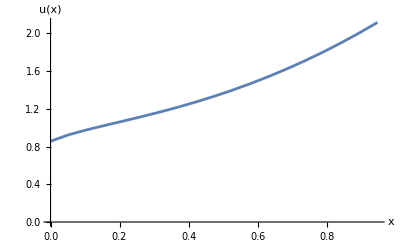

```mathematica
PlotTheTest[QuaData1 ]
```

Итерационный метод

```mathematica
IteData1 = Import["IterativeTest1.txt", "Table"];
```

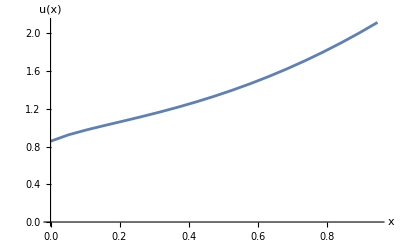

```mathematica
PlotTheTest[IteData1]
```

Сводный график

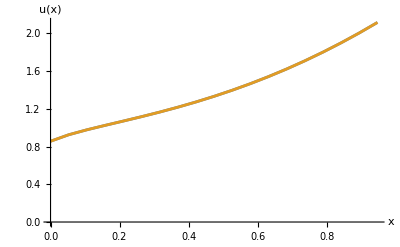

```mathematica
ComparePlotTheTest[IteData1, QuaData1]
```

## Тест вырожденного ядра

Вырожденное ядро

```mathematica
DegData1 = Import["DegenerateTest1.txt", "Table"];
```

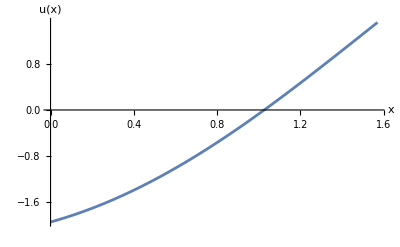

```mathematica
PlotTheTest[DegData1]
```